```mathematica
f[x]==x f[x-1]
```

f[x]==x f[-1+x]

```mathematica
Reduce[f[x]==x f[-1+x]]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[f[x]==x f[-1+x]]

```mathematica
Solve[f[x]==x f[x-1],f[x]]
```

{{f[x]→x f[-1+x]}}

```mathematica
Solve[f[x]==2f[x-1],f[x]]
```

{{f[x]→2 f[-1+x]}}

```mathematica
RSolve[{f[x]==2f[x-1],f[1]==1},f[x],x]
```

{{f[x]→2^(-1+x)}}

```mathematica
RSolve[{f[x]==2f[x-1],f[0]==1},f[x],x]
```

{{f[x]→2^x}}

```mathematica
RSolve[{f[x]==f[x-1]/x,f[0]==1},f[x],x]
```

{{f[x]→1/Pochhammer[2,-1+x]}}

```mathematica
1/Pochhammer[2,-1+x]
```

1/Pochhammer[2,-1+x]

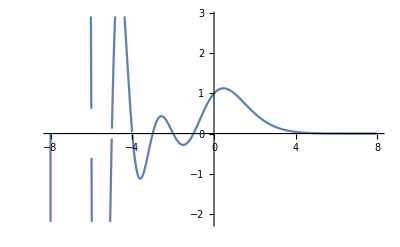

```mathematica
Plot[1/Pochhammer[2,-1+x],{x,-8,8}]
```

```mathematica
Pochhammer[2,-1+x]
```

Pochhammer[2,-1+x]

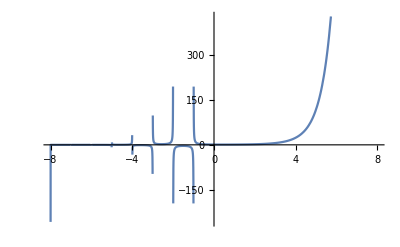

```mathematica
Plot[Pochhammer[2,-1+x],{x,-8,8}]
```

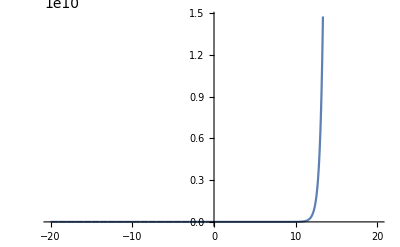

```mathematica
Plot[Pochhammer[2,-1+x],{x,-20,20}]
```

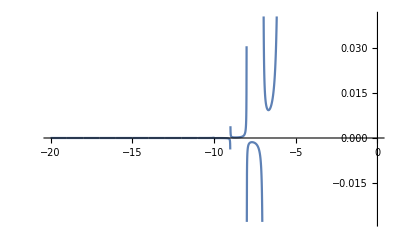

```mathematica
Plot[Pochhammer[2,-1+x],{x,-20,0}]
```

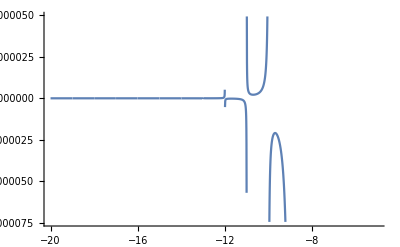

```mathematica
Plot[Pochhammer[2,-1+x],{x,-20,-5}]
```

```mathematica
RSolve[{f[x]==f[x-1]/2,f[0]==1},f[x],x]
```

{{f[x]→2^-x}}

```mathematica
RSolve[{f[x]==2f[x-1],f[0]==1},f[x],x]
```

{{f[x]→2^x}}

```mathematica
RSolve[{f[x]==f[x-1]-x,f[0]==1},f[x],x]
```

{{f[x]→1/2 (2-x-x^2)}}

```mathematica
RSolve[{f[x]==f[x-1]f[x-2],f[0]==1},f[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→ⅇ^(C[1] Fibonacci[x])},{f[x]→ⅇ^(C[1] Fibonacci[x]+ⅈ π LucasL[x])}}

```mathematica
RSolve[{f[x]==f[x-1]^x,f[0]==1},f[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→1}}

```mathematica
RSolve[{f[x]==f[x-1]^(1/x),f[0]==1},f[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→1}}

```mathematica
(1+Cos[π x])/2
```

1/2 (1+Cos[π x])

```mathematica
(1-(1+Cos[π x])/2)(3x+1)+((1+Cos[π x])/2)(x/2)
```

(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])

```mathematica
RSolve[{a[x]==(1+3 a[x-1]) (1+1/2 (-1-Cos[π a[x-1]]))+1/4 a[x-1] (1+Cos[π a[x-1]]),a[1]==1},a[x],x]
```

RSolve[{a[x]==(1+3 a[-1+x]) (1+1/2 (-1-Cos[π a[-1+x]]))+1/4 a[-1+x] (1+Cos[π a[-1+x]]),a[1]==1},a[x],x]